```mathematica
contador=Import["/home/battery/Documentos/mestrado/Spin_Ice/SPIN_ICE/mestrado/excitacao/rede5/num_lines.dat","Table"]
```

{{56884},{167},{6}}

```mathematica
{cont}=contador[[1]]
{nspins}=contador[[2]]
{nspins2}=contador[[3]]
```

{56884}

{167}

{6}

```mathematica
xy=Import["/home/battery/Documentos/mestrado/Spin_Ice/SPIN_ICE/mestrado/excitacao/rede5/xy.dat","Table"]
```

{{-6.,-6.},{-6.,-5.95},{-6.,-5.9},{-6.,-5.85},{-6.,-5.8},{-6.,-5.75},{-6.,-5.7},{-6.,-5.65},{-6.,-5.6},{-6.,-5.55},{-6.,-5.5},{-6.,-5.45},{-6.,-5.4},{-6.,-5.35},{-6.,-5.3},{-6.,-5.25},{-6.,-5.2},{-6.,-5.15},{-6.,-5.1},{-6.,-5.05},{-6.,-5.},{-6.,-4.95},{-6.,-4.9},{-6.,-4.85},{-6.,-4.8},{-6.,-4.75},{-6.,-4.7},{-6.,-4.65},{-6.,-4.6},{-6.,-4.55},{-6.,-4.5},«56822»,{6.,4.5},{6.,4.55},{6.,4.6},{6.,4.65},{6.,4.7},{6.,4.75},{6.,4.8},{6.,4.85},{6.,4.9},{6.,4.95},{6.,5.},{6.,5.05},{6.,5.1},{6.,5.15},{6.,5.2},{6.,5.25},{6.,5.3},{6.,5.35},{6.,5.4},{6.,5.45},{6.,5.5},{6.,5.55},{6.,5.6},{6.,5.65},{6.,5.7},{6.,5.75},{6.,5.8},{6.,5.85},{6.,5.9},{6.,5.95},{6.,6.}}

```mathematica
bxby=Import["/home/battery/Documentos/mestrado/Spin_Ice/SPIN_ICE/mestrado/excitacao/rede5/bxby.dat","Table"]
```

{{-0.0443029,-0.0319247},{-0.0451759,-0.031979},{-0.0460615,-0.0320204},{-0.0469595,-0.0320482},{-0.0478696,-0.0320618},{-0.0487918,-0.0320607},{-0.0497257,-0.0320441},{-0.050671,-0.0320114},«56868»,{-0.0327028,-0.0241555},{-0.0321257,-0.0240984},{-0.0315565,-0.0240345},{-0.0309954,-0.0239642},{-0.0304423,-0.0238877},{-0.0298973,-0.0238054},{-0.0293604,-0.0237174},{-0.0288316,-0.0236241}}

```mathematica
data=xy
```

{{-6.,-6.},{-6.,-5.95},{-6.,-5.9},{-6.,-5.85},{-6.,-5.8},{-6.,-5.75},{-6.,-5.7},{-6.,-5.65},{-6.,-5.6},{-6.,-5.55},{-6.,-5.5},{-6.,-5.45},{-6.,-5.4},{-6.,-5.35},{-6.,-5.3},{-6.,-5.25},{-6.,-5.2},{-6.,-5.15},{-6.,-5.1},{-6.,-5.05},{-6.,-5.},{-6.,-4.95},{-6.,-4.9},{-6.,-4.85},{-6.,-4.8},{-6.,-4.75},{-6.,-4.7},{-6.,-4.65},{-6.,-4.6},{-6.,-4.55},{-6.,-4.5},«56822»,{6.,4.5},{6.,4.55},{6.,4.6},{6.,4.65},{6.,4.7},{6.,4.75},{6.,4.8},{6.,4.85},{6.,4.9},{6.,4.95},{6.,5.},{6.,5.05},{6.,5.1},{6.,5.15},{6.,5.2},{6.,5.25},{6.,5.3},{6.,5.35},{6.,5.4},{6.,5.45},{6.,5.5},{6.,5.55},{6.,5.6},{6.,5.65},{6.,5.7},{6.,5.75},{6.,5.8},{6.,5.85},{6.,5.9},{6.,5.95},{6.,6.}}

```mathematica
Do[data[[i]]={xy[[i]],bxby[[i]]},{i,1,cont}]
```

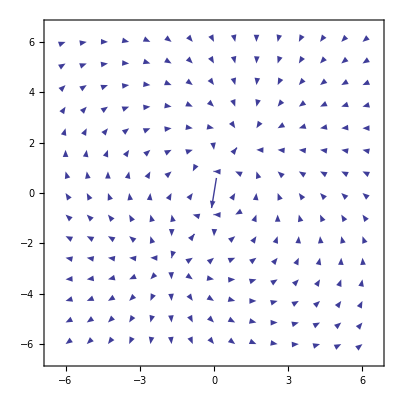

```mathematica
ListVectorPlot[data]
```

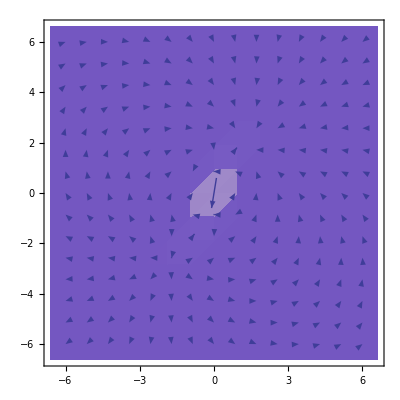

```mathematica
ListVectorDensityPlot[data]
```

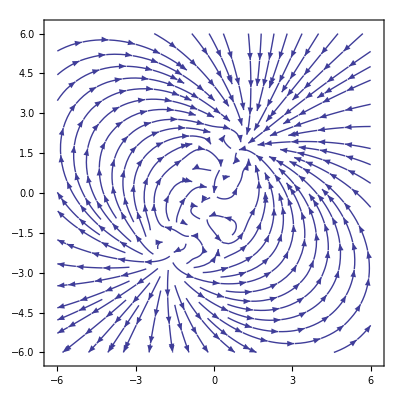

```mathematica
ListStreamPlot[data]
```

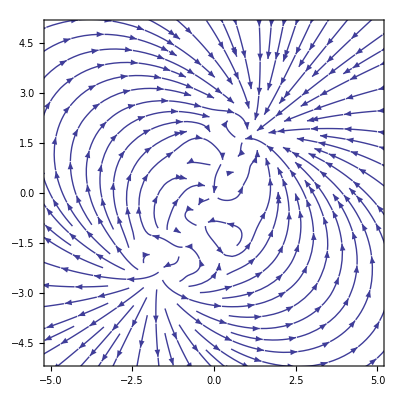

```mathematica
ListStreamPlot[data,PlotRange-> {{-5,5},{-5,5}}]
```

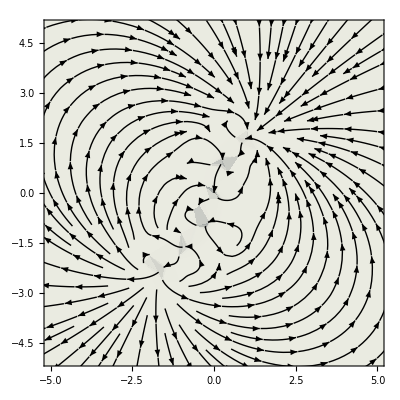

```mathematica
ListStreamDensityPlot[data,StreamStyle-> Black,ColorFunction-> "GrayTones",ColorFunctionScaling-> {1,0},PlotRange->{{-5,5},{-5,5}}]
```

```mathematica
sxyi=Import["/home/battery/Documentos/mestrado/Spin_Ice/SPIN_ICE/mestrado/excitacao/rede5/sxsy_ini.dat","Table"]
```

{{-3.31865,-4.04808},{-3.51147,-2.78205},{-2.73205,-3.13205},{-2.78205,-3.31865},{-3.13205,-4.09808},{-4.01147,-1.81603},{-3.31865,-1.31603},{-2.81865,-0.45},{-2.73205,0.4},{-3.18205,-1.27942},{-2.33205,-1.36603},{-3.18205,-1.45263},{-2.81865,-2.28205},{-4.01147,0.916025},{-3.31865,1.41603},{-3.51147,2.68205},{-2.73205,2.33205},{-3.18205,1.45263},{-2.33205,1.36603},{-3.18205,1.27942},{-3.51147,0.05},{-4.01147,3.64808},{-3.13205,4.09808},{-2.78205,3.31865},{-2.81865,3.18205},{-2.28205,-4.01147},{-1.95263,-2.78205},{-1.81603,-2.74365},{-1.45263,-3.64808},{-1.36603,-4.49808},{-1.27942,-3.64808},{-1.31603,-3.51147},{-0.966025,-2.73205},{-0.0866025,-3.18205},{-2.44929×10^-17,-2.33205},{-0.05,-3.31865},{-0.4,-4.09808},{-2.64545,-2.28205},{-2.68205,-2.14545},{-2.68205,-0.586603},{-2.64545,-0.45},{-1.81603,-0.0116025},{-2.14545,-1.31603},{-1.45263,-1.81603},{-1.41603,-1.95263},{-1.31603,-1.95263},{-0.586603,-1.41603},{-1.36603,-0.966025},{-0.586603,-1.31603},{-1.31603,-0.779423},{-0.966025,-4.89859×10^-17},{-0.779423,-0.05},{-2.44929×10^-17,0.4},{-0.05,-0.586603},{0.4,-1.36603},{-0.45,-1.45263},{-0.779423,-2.68205},{-1.95263,0.05},{-2.68205,0.586603},{-2.68205,2.14545},{-1.95263,2.68205},{-1.41603,2.02763},{-2.14545,1.41603},{-1.45263,0.916025},{-1.81603,0.0866025},{-1.31603,0.779423},{-1.27942,0.916025},{-1.36603,1.76603},{-0.586603,1.41603},{-0.916025,2.64545},{-1.76603,2.73205},{-0.779423,2.68205},{-2.44929×10^-17,2.33205},{-0.45,1.45263},{0.4,1.36603},{-0.45,1.27942},{-0.0866025,0.45},{-2.64545,3.18205},{-2.28205,4.01147},{-1.45263,3.64808},{-1.41603,3.51147},{-0.916025,2.81865},{-1.27942,3.64808},{-1.36603,4.49808},{0.4,4.09808},{-0.45,4.01147},{-0.0866025,3.18205},{0.45,-4.01147},{0.0866025,-3.18205},{1.31603,-3.43647},{1.27942,-3.64808},{1.36603,-4.49808},{1.45263,-3.64808},{1.81603,-2.81865},{0.966025,-2.73205},{2.64545,-3.18205},{2.73205,-2.33205},{2.68205,-3.31865},{2.33205,-4.09808},{0.779423,-2.68205},{0.05,-2.14545},{0.05,-0.586603},{0.779423,-0.05},{0.916025,-0.0116025},{0.586603,-1.31603},{1.27942,-1.81603},{1.31603,-1.95263},{1.81603,-2.64545},{1.45263,-1.81603},{1.36603,-0.966025},{2.14545,-1.31603},{1.41603,-0.779423},{1.76603,-4.89859×10^-17},{1.95263,-0.05},{2.73205,-0.4},{2.28205,-1.27942},{3.13205,-1.36603},{2.28205,-1.45263},{1.95263,-2.68205},{0.0866025,0.45},{0.45,1.27942},{0.05,2.14545},{0.779423,2.68205},{1.31603,2.02763},{1.27942,1.81603},{1.27942,0.916025},{0.916025,0.0866025},{1.41603,0.779423},{1.45263,0.916025},{1.36603,1.76603},{2.14545,1.41603},{1.81603,2.64545},{0.966025,2.73205},{2.64545,2.28205},{2.73205,3.13205},{2.28205,1.45263},{3.13205,1.36603},{2.28205,1.27942},{2.64545,0.45},{0.0866025,3.18205},{0.05,3.31865},{0.586603,4.04808},{1.31603,3.51147},{1.81603,2.81865},{2.14545,4.04808},{1.36603,3.69808},{2.33205,4.09808},{2.68205,3.31865},{1.95263,2.78205},{3.18205,-4.01147},{2.81865,-3.18205},{4.01147,-3.64808},{3.51147,-2.68205},{2.78205,-2.14545},{2.78205,-0.586603},{3.51147,-0.05},{4.01147,-0.916025},{3.31865,-1.41603},{2.81865,0.45},{2.78205,0.586603},{2.78205,2.14545},{2.81865,2.28205},{3.31865,1.41603},{4.01147,0.916025},{3.51147,2.78205},{3.18205,4.01147},{4.01147,3.64808}}

```mathematica
sxyf=Import["/home/battery/Documentos/mestrado/Spin_Ice/SPIN_ICE/mestrado/excitacao/rede5/sxsy_end.dat","Table"]
```

{{-4.01147,-3.64808},{-2.81865,-3.18205},{-2.73205,-2.33205},{-3.18205,-4.01147},{-2.33205,-4.09808},{-3.31865,-1.41603},{-4.01147,-0.916025},{-3.51147,-0.05},{-2.73205,-0.4},{-2.78205,-0.586603},{-3.13205,-1.36603},{-2.78205,-2.14545},{-3.51147,-2.68205},{-3.31865,1.31603},{-4.01147,1.81603},{-2.81865,2.28205},{-2.73205,3.13205},{-2.78205,2.14545},{-3.13205,1.36603},{-2.78205,0.586603},{-2.81865,0.45},{-3.31865,4.04808},{-2.33205,4.09808},{-3.18205,4.01147},{-3.51147,2.78205},{-2.68205,-3.31865},{-2.64545,-3.18205},{-1.41603,-3.43647},{-2.14545,-4.04808},{-1.36603,-3.69808},{-0.586603,-4.04808},{-0.916025,-2.81865},{-1.76603,-2.73205},{-0.779423,-2.78205},{2.44929×10^-17,-3.13205},{-0.45,-4.01147},{0.4,-4.09808},{-1.95263,-2.68205},{-2.28205,-1.45263},{-2.28205,-1.27942},{-1.95263,-0.05},{-1.41603,-0.704423},{-1.45263,-0.916025},{-2.14545,-1.41603},{-1.81603,-2.64545},{-0.916025,-2.64545},{-1.27942,-1.81603},{-1.36603,-1.76603},{-1.27942,-0.916025},{-0.916025,-0.0866025},{-1.76603,4.89859×10^-17},{-0.0866025,-0.45},{2.44929×10^-17,-0.4},{-0.45,-1.27942},{-0.4,-1.36603},{-0.05,-2.14545},{-0.0866025,-2.28205},{-2.64545,0.45},{-2.28205,1.27942},{-2.28205,1.45263},{-2.64545,2.28205},{-1.81603,2.72045},{-1.45263,1.81603},{-2.14545,1.31603},{-1.41603,0.779423},{-0.916025,0.0866025},{-0.586603,1.31603},{-1.36603,0.966025},{-1.27942,1.81603},{-1.31603,1.95263},{-0.966025,2.73205},{-0.0866025,2.28205},{2.44929×10^-17,3.13205},{-0.05,2.14545},{-0.4,1.36603},{-0.05,0.586603},{-0.779423,0.05},{-1.95263,2.78205},{-2.68205,3.31865},{-2.14545,4.04808},{-1.81603,2.81865},{-1.31603,3.51147},{-0.586603,4.04808},{-1.36603,3.69808},{-0.4,4.09808},{-0.05,3.31865},{-0.779423,2.78205},{0.05,-3.31865},{0.779423,-2.78205},{0.916025,-2.74365},{0.586603,-4.04808},{1.36603,-3.69808},{2.14545,-4.04808},{1.41603,-3.51147},{1.76603,-2.73205},{1.95263,-2.78205},{2.73205,-3.13205},{2.28205,-4.01147},{3.13205,-4.09808},{0.0866025,-2.28205},{0.45,-1.45263},{0.45,-1.27942},{0.0866025,-0.45},{1.31603,-0.704423},{1.27942,-0.916025},{0.586603,-1.41603},{0.916025,-2.64545},{1.41603,-1.95263},{2.14545,-1.41603},{1.36603,-1.76603},{1.45263,-0.916025},{1.81603,-0.0866025},{0.966025,4.89859×10^-17},{2.64545,-0.45},{2.73205,0.4},{2.68205,-0.586603},{2.33205,-1.36603},{2.68205,-2.14545},{2.64545,-2.28205},{0.779423,0.05},{0.05,0.586603},{0.45,1.45263},{0.0866025,2.28205},{0.916025,2.72045},{0.586603,1.41603},{0.586603,1.31603},{1.31603,0.779423},{1.81603,0.0866025},{2.14545,1.31603},{1.36603,0.966025},{1.45263,1.81603},{1.41603,1.95263},{1.76603,2.73205},{1.95263,2.68205},{2.73205,2.33205},{2.68205,2.14545},{2.33205,1.36603},{2.68205,0.586603},{1.95263,0.05},{0.779423,2.78205},{0.45,4.01147},{1.27942,3.64808},{0.916025,2.81865},{1.41603,3.51147},{1.45263,3.64808},{1.36603,4.49808},{3.13205,4.09808},{2.28205,4.01147},{2.64545,3.18205},{2.78205,-3.31865},{3.51147,-2.78205},{3.31865,-4.04808},{2.81865,-2.28205},{3.18205,-1.45263},{3.18205,-1.27942},{2.81865,-0.45},{3.31865,-1.31603},{4.01147,-1.81603},{3.51147,0.05},{3.18205,1.27942},{3.18205,1.45263},{3.51147,2.68205},{4.01147,1.81603},{3.31865,1.31603},{2.81865,3.18205},{2.78205,3.31865},{3.31865,4.04808}}

```mathematica
rede=sxyi
```

{{-3.31865,-4.04808},{-3.51147,-2.78205},{-2.73205,-3.13205},{-2.78205,-3.31865},{-3.13205,-4.09808},{-4.01147,-1.81603},{-3.31865,-1.31603},{-2.81865,-0.45},{-2.73205,0.4},{-3.18205,-1.27942},{-2.33205,-1.36603},{-3.18205,-1.45263},{-2.81865,-2.28205},{-4.01147,0.916025},{-3.31865,1.41603},{-3.51147,2.68205},{-2.73205,2.33205},{-3.18205,1.45263},{-2.33205,1.36603},{-3.18205,1.27942},{-3.51147,0.05},{-4.01147,3.64808},{-3.13205,4.09808},{-2.78205,3.31865},{-2.81865,3.18205},{-2.28205,-4.01147},{-1.95263,-2.78205},{-1.81603,-2.74365},{-1.45263,-3.64808},{-1.36603,-4.49808},{-1.27942,-3.64808},{-1.31603,-3.51147},{-0.966025,-2.73205},{-0.0866025,-3.18205},{-2.44929×10^-17,-2.33205},{-0.05,-3.31865},{-0.4,-4.09808},{-2.64545,-2.28205},{-2.68205,-2.14545},{-2.68205,-0.586603},{-2.64545,-0.45},{-1.81603,-0.0116025},{-2.14545,-1.31603},{-1.45263,-1.81603},{-1.41603,-1.95263},{-1.31603,-1.95263},{-0.586603,-1.41603},{-1.36603,-0.966025},{-0.586603,-1.31603},{-1.31603,-0.779423},{-0.966025,-4.89859×10^-17},{-0.779423,-0.05},{-2.44929×10^-17,0.4},{-0.05,-0.586603},{0.4,-1.36603},{-0.45,-1.45263},{-0.779423,-2.68205},{-1.95263,0.05},{-2.68205,0.586603},{-2.68205,2.14545},{-1.95263,2.68205},{-1.41603,2.02763},{-2.14545,1.41603},{-1.45263,0.916025},{-1.81603,0.0866025},{-1.31603,0.779423},{-1.27942,0.916025},{-1.36603,1.76603},{-0.586603,1.41603},{-0.916025,2.64545},{-1.76603,2.73205},{-0.779423,2.68205},{-2.44929×10^-17,2.33205},{-0.45,1.45263},{0.4,1.36603},{-0.45,1.27942},{-0.0866025,0.45},{-2.64545,3.18205},{-2.28205,4.01147},{-1.45263,3.64808},{-1.41603,3.51147},{-0.916025,2.81865},{-1.27942,3.64808},{-1.36603,4.49808},{0.4,4.09808},{-0.45,4.01147},{-0.0866025,3.18205},{0.45,-4.01147},{0.0866025,-3.18205},{1.31603,-3.43647},{1.27942,-3.64808},{1.36603,-4.49808},{1.45263,-3.64808},{1.81603,-2.81865},{0.966025,-2.73205},{2.64545,-3.18205},{2.73205,-2.33205},{2.68205,-3.31865},{2.33205,-4.09808},{0.779423,-2.68205},{0.05,-2.14545},{0.05,-0.586603},{0.779423,-0.05},{0.916025,-0.0116025},{0.586603,-1.31603},{1.27942,-1.81603},{1.31603,-1.95263},{1.81603,-2.64545},{1.45263,-1.81603},{1.36603,-0.966025},{2.14545,-1.31603},{1.41603,-0.779423},{1.76603,-4.89859×10^-17},{1.95263,-0.05},{2.73205,-0.4},{2.28205,-1.27942},{3.13205,-1.36603},{2.28205,-1.45263},{1.95263,-2.68205},{0.0866025,0.45},{0.45,1.27942},{0.05,2.14545},{0.779423,2.68205},{1.31603,2.02763},{1.27942,1.81603},{1.27942,0.916025},{0.916025,0.0866025},{1.41603,0.779423},{1.45263,0.916025},{1.36603,1.76603},{2.14545,1.41603},{1.81603,2.64545},{0.966025,2.73205},{2.64545,2.28205},{2.73205,3.13205},{2.28205,1.45263},{3.13205,1.36603},{2.28205,1.27942},{2.64545,0.45},{0.0866025,3.18205},{0.05,3.31865},{0.586603,4.04808},{1.31603,3.51147},{1.81603,2.81865},{2.14545,4.04808},{1.36603,3.69808},{2.33205,4.09808},{2.68205,3.31865},{1.95263,2.78205},{3.18205,-4.01147},{2.81865,-3.18205},{4.01147,-3.64808},{3.51147,-2.68205},{2.78205,-2.14545},{2.78205,-0.586603},{3.51147,-0.05},{4.01147,-0.916025},{3.31865,-1.41603},{2.81865,0.45},{2.78205,0.586603},{2.78205,2.14545},{2.81865,2.28205},{3.31865,1.41603},{4.01147,0.916025},{3.51147,2.78205},{3.18205,4.01147},{4.01147,3.64808}}

```mathematica
sxyflipi=Import["/home/battery/Documentos/mestrado/Spin_Ice/SPIN_ICE/mestrado/excitacao/rede5/sxsy_flip_ini.dat","Table"]
```

{{-1.41603,-1.95263},{-0.586603,-1.41603},{-0.05,-0.586603},{-2.44929×10^-17,0.4},{0.45,1.27942},{1.27942,1.81603}}

```mathematica
sxyflipf=Import["/home/battery/Documentos/mestrado/Spin_Ice/SPIN_ICE/mestrado/excitacao/rede5/sxsy_flip_end.dat","Table"]
```

{{-1.81603,-2.64545},{-1.27942,-1.81603},{-0.45,-1.27942},{2.44929×10^-17,-0.4},{0.05,0.586603},{0.586603,1.41603}}

```mathematica
rede2=sxyflipi
```

{{-1.41603,-1.95263},{-0.586603,-1.41603},{-0.05,-0.586603},{-2.44929×10^-17,0.4},{0.45,1.27942},{1.27942,1.81603}}

```mathematica
Do[rede[[i]]={sxyi[[i]],sxyf[[i]]},{i,1,nspins}]
Do[rede2[[i]]={sxyflipi[[i]],sxyflipf[[i]]},{i,1,nspins2}]
```

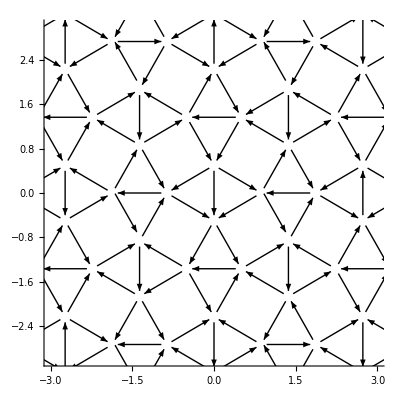

```mathematica
Graphics[Table[Arrow[rede[[i]]],{i,1,nspins}],Axes-> True,PlotRange-> {{-3,3},{-3,3}}]
```

```mathematica
rgbnum:=.97
thick:=0.008
opcarr:=0.4
opcflip:=0.6
arrowh:=0.05
Rasterize[Show[ListStreamDensityPlot[data,DataRange->{{-4.,4.},{-4.,4.}},StreamStyle-> Black,ColorFunction-> "GrayTones",ColorFunctionScaling->{1,0},Background-> RGBColor[rgbnum,rgbnum,rgbnum]],
Graphics[{Thickness[thick],Opacity[opcarr],Arrowheads[arrowh],Table[Arrow[rede[[i]]],{i,1,nspins}]}], 
Graphics[{Thickness[thick],Opacity[opcflip],Arrowheads[arrowh],Red,Table[Arrow[rede2[[i]]],{i,1,nspins2}]}]  ]  ,RasterSize-> 4000  ]
```

-Graphics-

```mathematica
Export["linefield_excitation_snub_l20.eps",-Graphics-]
```

linefield_excitation_snub_l20.eps